# Three Side Distribution Problem

```mathematica
Remove["Global`*"]; (* 初始化 *)
```

## 初始化几何参量

```mathematica
originalPoint = {0,0,0}; (* 原点坐标 *)
groundVec = {0,0,1}; (* 地面法向量 *)
diameter = 10; (* 圆柱直径 *)
```

## 不考虑所有的运动碰撞 仅考虑圆柱的朝向对最终落地的影响

```mathematica
n[θ_,φ_]={Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ]}; (* 圆柱法向量 *)
```

对上面的角度分布, 圆柱可能的落点有以下的可能性 :

```mathematica
Map[
Module[{
cylinderHeight,(* 圆柱高度 *)
forward, (* 圆柱指向向量 *)
cylinderOriginal (* 圆柱的位置 *)
},
cylinderHeight = 10;
forward=n[RandomReal[{#[[1]], #[[2]]}],RandomReal[{0,0}]];
cylinderOriginal = {0,0,Sin[ArcCos[groundVec.forward]]*diameter/2};
Graphics3D[{
(* 画出地面法向量 *)
{Blue,Thick,Arrow[{cylinderOriginal,
cylinderOriginal+2*cylinderHeight*groundVec}]},
(* 画出圆柱指向向量 *)
{Red,Thick,Arrow[{cylinderOriginal,
cylinderOriginal+2*cylinderHeight*forward}]},
(* 画出重心指向向量 *)
{Black, Thick, Arrow[{cylinderOriginal+cylinderHeight/2*forward,
cylinderOriginal+cylinderHeight/2*forward-cylinderHeight*groundVec}]},
(* 画出圆柱 *)
{Yellow,Opacity[0.5],Cylinder[{cylinderOriginal,
cylinderOriginal+cylinderHeight*forward},diameter/2]}
},
ViewPoint->Front,(* 从正面观察 *)
PlotLabel->#[[3]]] (* 标题 *)
]&,
{
{0,π/2,"随机分布"}, (* 出于对称性, 只需考虑forward指向历遍上半球面的分布 *)
{0,π/4,"顶面朝上"}, (* 下面两种情况是提前计算过的, 具体的计算方法在下面介绍 *)
{π/4,π/2,"侧面朝上"}
}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

根据圆柱的重心相对和地面接触接触点的相对位置来判断落到地面后朝上面的种类 .  可以发现, 当重心向量通过底面的时候, 圆柱最后的正面朝上, 当重心向量通过侧面的时候, 圆柱最后侧面朝上 . 于是发现当d << H的时候, 落在侧面的可能性更大, 当d >> H的时候, 落在顶面或者底面的可能性更大 .

```mathematica
h = 10;(* 程序里面的圆柱高度常数 *)
β[d_]=ArcTan[h /(d)];
p[d_]=Integrate[ (* 计算落在顶面的可能性 *)
If[π/2-(θ+β[d]) > 0,1,0] Sin[θ],
{θ,0,π/2},{φ,0,2π}
]/(4π);
```

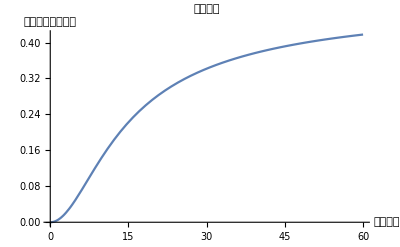

```mathematica
(* 绘制出落在顶面的可能性和高度的关系 *)
theoryPlot=Plot[p[d],{d,0,60},PlotRange->All,
AxesLabel->{"圆柱直径","顶面朝上的可能性"},
PlotLabel->"理论数据"]
```

观察绘制出来的图形, 当h -> 0 的时候, 落在顶面和底面的可能性相等并且之和为1, 当h -> ∞的时候, 落在顶面和底面的可能性趋于零, 落在侧边 .

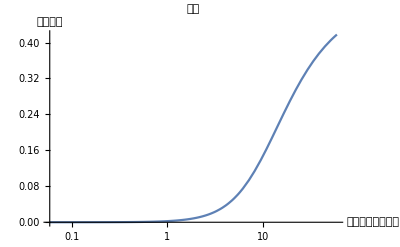

```mathematica
LogLinearPlot[p[d],{d,0,60},PlotRange->All,
AxesLabel->{"顶面朝上的可能性","圆柱直径"},
PlotLabel->"指数"]
```

结果看起来好像是个和指数相关的东西, 大概吧 .

```mathematica
Solve[p[d]==1/3,d]//N
```

{{d→28.2843}}

并且上面的大概就是三面可能性相等的情况吧 . (怎么感觉和模拟的结果有点不一样啊 ...)

## 通过计算机进行模拟 对理论模型进行检验

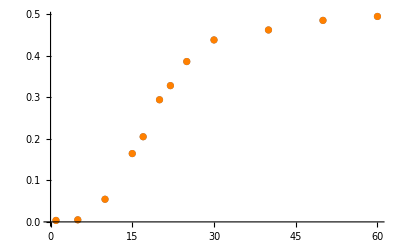

```mathematica
(* 模拟的数据 *)
simulateData ={
(* 数据: 直径, 顶面朝上次数, 底面朝上次数, 侧面朝上次数 *)
{1,7, 2, 1991},
{5,10,1,1989 },
{10,109,91,1800},
{15,329,325,1346},
{17,410,412,1178},
{20,588,599,813},
{22,656,680,664},
{25,772,770,458},
{30,876,860,264},
{40,924,968,108},
{50,970,979,51},
{60,989,979,32}
};
simulateDataPlot=ListPlot[
Map[Style[{#[[1]],#[[2]]/(#[[2]]+#[[3]]+#[[4]])},Orange]&,
simulateData]]
```

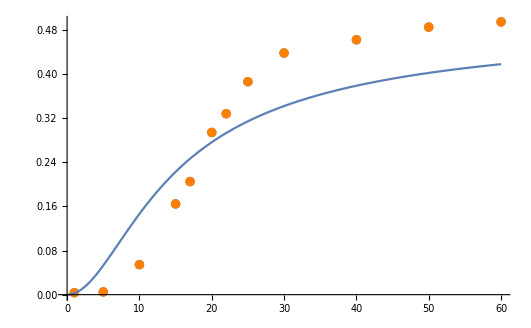

```mathematica
Show[{simulateDataPlot,theoryPlot}]
```

可以发现, 模拟实验和理论吻合情况一般, 虽然都呈现出S型趋势, 但是在后半部分有较大的偏离, 可能的原因 :
 1. 实验中抛出的圆柱间距太小, 相互之间发生了碰撞和干扰, 导致了向下倒的可能性更大, 所以影响了后半部分 ; 
2. 理论模型中没有考虑由于和底面有一定初速度的反弹而导致的影响, 需要更进一步的分析 .

将程序中两两圆柱之间的间距从10 (MM) 修改为100 (MM) 以减少相互之间的干扰, 得到新的模拟数据 :

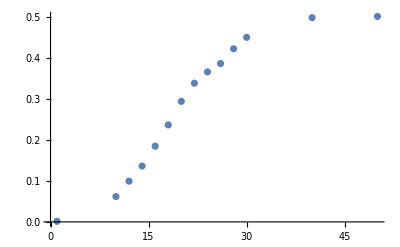

```mathematica
newSimulateData={
(* 数据: 直径, 顶面朝上次数, 底面朝上次数, 侧面朝上次数 *)
{1,3,0,1997},
{10,124,69,1807},
{12,199,187,1614},
{14,273,258,1469},
{16,370,341,1289},
{18,474,460,1066},
{20,589,564,847},
{22,678,683,639},
{24,733,728,539},
{26,774,785,441},
{28,846,786,368},
{30,902,863,235},
{40,998,902,100},
{50,1004,952,44}
};
newSimulateDataPlot=ListPlot[
Map[{#[[1]],#[[2]]/(#[[2]]+#[[3]]+#[[4]])}&,
newSimulateData]]
```

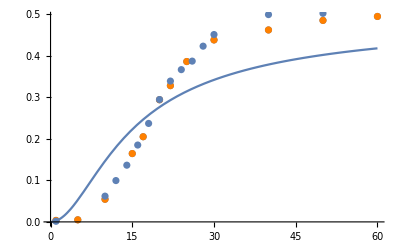

```mathematica
Show[{simulateDataPlot,newSimulateDataPlot,theoryPlot}]
```

发现相互碰撞的影响应该是比较少的